Importing and Exporting

Everything we’ve done so far in this book has been done entirely within the Wolfram Language and the Wolfram Knowledgebase. But sometimes you need to get things from the outside. Needless to say, they often won’t be as clean and organized as what we’re used to inside the Wolfram Language—and they may change without warning.

As a first example, let’s import the text from the front page of the United Nations website. We can do this using the function Import.

Import a text version of the front page of the UN website (it might be different now):

```mathematica
Import["http://un.org"]
```

الأمم المتحدة — إنها عالمك  
联合国，您的世界！  
United Nations — It's your world!  
Nations Unies — C'est votre monde!  
Организация Объединенных Наций — это ваш мир!  
Las Naciones Unidas son su mundo

The result is a string, possibly with some blank lines. Let’s start by splitting the string at newlines.

Split at newlines to get a list of strings:

```mathematica
StringSplit[Import["http://un.org"],"\n"]
```

{الأمم المتحدة — إنها عالمك, 联合国，您的世界！,United Nations — It's your world!,Nations Unies — C'est votre monde!,Организация Объединенных Наций — это ваш мир!,Las Naciones Unidas son su mundo}

Identify the language for each string (blank lines are considered English):

```mathematica
LanguageIdentify[StringSplit[Import["http://un.org"],"\n"]]
```

{Arabic,Chinese,English,French,Russian,Spanish}

Import lets you import a wide variety of different elements. "Hyperlinks" gets hyperlinks that appear on a webpage; "Images" gets images.

Get a list of the hyperlinks on the front of the UN website:

```mathematica
Import["http://un.org","Hyperlinks"]
```

{//www.un.org/ar/index.html,//www.un.org/zh/index.html,//www.un.org/en/index.html,//www.un.org/fr/index.html,//www.un.org/ru/index.html,//www.un.org/es/index.html}

Get the images on the front page of Wikipedia:

```mathematica
Import["http://wikipedia.org","Images"]
```

{-Graphics-,-Graphics-}

As a more sophisticated example, here’s a graph of the hyperlinks in part of my website. To keep it manageable, I’ve taken just the first 5 hyperlinks at each level, and gone only 3 levels.

Compute part of the hyperlink graph for my website:

```mathematica
NestGraph[Take[Import[#,"Hyperlinks"],5]&,"http://stephenwolfram.com",3]
```

-Graphics-

The Wolfram Language can import hundreds of formats—including spreadsheets, images, sounds, geometry, databases, log files and more. Import will automatically look at the file extension (.png, .xls, etc.) to determine what to do.

Import a picture from my website:

```mathematica
Import["http://www.stephenwolfram.com/img/homepage/stephen-wolfram-portrait.png"]
```

-Graphics-

The Wolfram Language recognizes me!

```mathematica
Classify["NotablePerson",%]
```

Stephen Wolfram

As well as importing from the web, Import can also import from your own files, stored in your computer system or in the Wolfram Cloud.

The Wolfram Language lets you not only deal with webpages and files, but also with services or APIs. For example, SocialMediaData lets you get data from social media services—at least once you’ve authorized them to send the data.

Find the network of my Facebook friends who give access to their connection data:

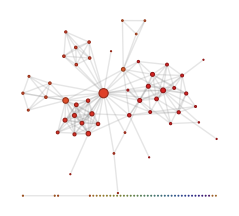

```mathematica
SocialMediaData["Facebook","FriendNetwork"]
```

Another external service the Wolfram Language can access is web search.

Search for images on the web using the keywords “colorful birds”:

```mathematica
WebImageSearch["colorful birds"]
```

Dataset[<>]

Request image thumbnails:

```mathematica
WebImageSearch["colorful birds","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

They’re recognized as different kinds of birds:

```mathematica
ImageIdentify/@%
```

{indigo bunting,blue peafowl,mandarin duck,european goldfinch,rainbow lorikeet,ring-necked parakeet,bluebird,rainbow lorikeet,scrub-bird,rainbow lorikeet}

An important source of external data for the Wolfram Language is the Wolfram Data Repository. The data in this repository comes from many places—but it’s all been set up to be easy to work with in the Wolfram Language.

You can find out what’s available by browsing the Wolfram Data Repository.

-Graphics-

Once you've found something you want, just use ResourceData["name"] to get it into the Wolfram Language.

Get the full text of Darwin’s On the Origin of Species, then make a word cloud of it:

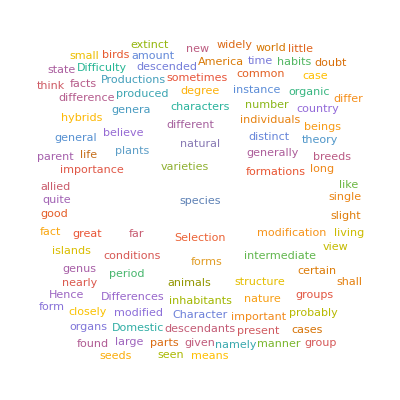

```mathematica
WordCloud[ResourceData["On the Origin of Species"]]
```

In addition to getting things into the Wolfram Language, you can also send things out. For example, SendMail sends email from the Wolfram Language.

Send oneself a message by email (for me it’s sending to me):

```mathematica
SendMail["Hello from the Wolfram Language!"]
```

-Graphics-

Send email to a test account with subject “Wolf” and a picture of a wolf attached:

```mathematica
SendMail["test@wolfram.com",{"Wolf","Here's a wolf...", -Graphics-}]
```

If you want to interact with external programs and services, you’ll often have to export things from the Wolfram Language.

Export a graphic of a circle to the cloud in PDF format:

```mathematica
CloudExport[Graphics[Circle[ ]],"PDF"]
```

CloudObject[]

You can also export to local files using Export.

Export a table of primes and their powers to a local spreadsheet file:

```mathematica
Export["primepowers.xls",Table[Prime[m]^n,{m,10},{n,4}]]
```

primepowers.xls

Here’s part of the resulting file:

-Graphics-

Import the contents of the file back into the Wolfram Language:

```mathematica
Import["primepowers.xls"]
```

{{{2.,4.,8.,16.},{3.,9.,27.,81.},{5.,25.,125.,625.},{7.,49.,343.,2401.},{11.,121.,1331.,14641.},{13.,169.,2197.,28561.},{17.,289.,4913.,83521.},{19.,361.,6859.,130321.},{23.,529.,12167.,279841.},{29.,841.,24389.,707281.}}}

The Wolfram Language can import and export hundreds of formats, of many different kinds.

Export 3D geometry in a format suitable for 3D printing:

```mathematica
Export["spikey.stl",LinguisticAssistant["Image"]]
```

spikey.stl

Here’s the result of 3D printing from the spikey.stl file:

-Graphics-

Creating 3D geometry in a form suitable for printing can be quite complicated. The function Printout3D does all the steps automatically—and it can also send the final geometry to a 3D printing service (or to your own 3D printer, if you have one).

Make a random clump of spheres:

```mathematica
Graphics3D[Sphere[RandomReal[5,{30,3}]]]
```

-Graphics3D-

Send this for 3D printing to the Sculpteo service:

```mathematica
Printout3D[%,"Sculpteo"]
```

Dataset[<>]

-Graphics- |     | -Graphics-

Vocabulary

Import[loc] |   | import from an external location
SocialMediaData[...] |   | get data from social media networks
WebImageSearch["keyword"] |   | do an image search on the web
ResourceData["name"] |   | get data from the Wolfram Data Repository
SendMail[expr] |   | send email
CloudExport[expr,format] |   | export in a certain format to the cloud
Export[file,expr] |   | export to a file
Printout3D[source,"service"] |   | send source to a 3D printer service

"9 Exercises Available" | "Get Started »"

Import the images from http://google.com. »

| Sample expected output: |  
  | {-Graphics-,-Graphics-} |

Make an image collage of disks with the dominant colors from images on http://google.com. »

| Sample expected output: |  
  | -Graphics- |

Make a word cloud of the text on http://bbc.co.uk. »

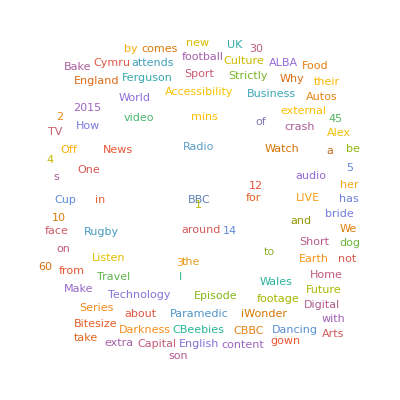
| Sample expected output: |  
  | -Graphics- |

Make an image collage of the images on http://nps.gov. »

| Sample expected output: |  
  | -Graphics- |

Use ImageInstanceQ to find pictures on https://en.wikipedia.org/wiki/Ostrich that are of birds. »

| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use TextCases with "Country" to find instances of country names on http://nato.int, and make a word cloud of them. »

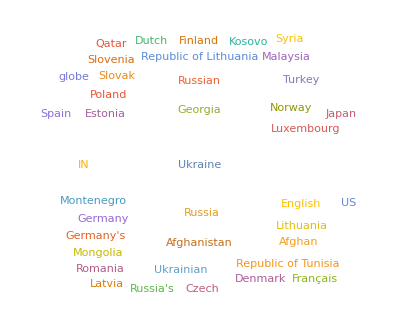
| Sample expected output: |  
  | -Graphics- |

Find the number of links on https://en.wikipedia.org. »

| Sample expected output: |  
  | 292 |

Send yourself mail with a map of your current location. »

| Sample expected output: |  
  | {"MessageID"→"27542834033679034197.0.WolframLanguage.7Qo3YdBo"} |

Send yourself mail with an icon of the current phase of the moon. »

| Sample expected output: |  
  | {"MessageID"→"27542858880723918541.0.WolframLanguage.7Qo3YdBo"} |

Q&A

Why do I get different results when I run the website examples?

Because the websites have changed!  You’ll get whatever they have on them now.

Why doesn’t Import retrieve elements that I see when I visit a webpage in a browser?

Probably because they’re not directly present in the HTML source of the webpage, which is what Import looks at. They’re probably being dynamically added using JavaScript.

Can I import a local file from my computer if I’m using the cloud?

Yes. Use the upload  button in the cloud system to upload the file into your cloud file system, then
use Import.

What formats can Import handle?

See the list at wolfr.am/ref-importexport or evaluate $ImportFormats.

How do Import and Export figure out what format to use?

You can explicitly tell them. Or they can determine it from file extensions, like .gif or .mbox.

Where does Export put the files it creates?

If you don’t give a directory in the file name you specify, it’ll go in your current directory. You can open it as your operating system would using SystemOpen, and you can delete it with DeleteFile.

What is an API?

An application program interface. It’s an interface that a program exposes to other programs, rather than to humans. The Wolfram Language has several APIs, and lets you create your own using APIFunction.

How do I authorize a connection to an external account of mine?

When you use SocialMediaData or ServiceConnect, you’ll typically be prompted to authorize the Wolfram Connection app for that particular service.

Tech Notes

ImportString lets you “import” from a string rather than from an external file or URL. ExportString “exports” to a string.

SendMail uses either mail server preferences you set up, or a proxy in the Wolfram Cloud.

The Wolfram Language supports many external services. Typically it uses mechanisms like OAuth to authenticate them.

Another way to get (and send) data is through direct connection from your computer to a sensor, Arduino, etc. The Wolfram Language has a whole framework for dealing with such things, including functions such as DeviceReadTimeSeries.

If you’re running everything locally on your computer, you can have the Wolfram Language start external programs, and exchange data with them, for example using RunProcess. In simple cases, you’ll often be able to just pipe data straight in from a program, say with Import["!program",...].

The Wolfram Language supports asynchronous reading and writing of data. A simple case is URLSubmit, but ChannelListen, etc. allow you to set up a complete brokered publish-subscribe system.

More to Explore

Guide to Importing and Exporting in the Wolfram Language »